## Implemented Functions

```mathematica
inputFile[fileName_]:=BinaryReadList[FileNameJoin[{NotebookDirectory[],fileName}]];
```

```mathematica
color[bytes_]:=Piecewise[{{White,bytes==255},{Black,bytes==0},{Blue,32≤bytes≤126},{Green,1≤bytes≤31}},Red];
```

```mathematica
color[x]
```

Piecewise[{{GrayLevel[1], x==255}, {GrayLevel[0], x==0}, {RGBColor[0, 0, 1], 32≤x≤126}, {RGBColor[0, 1, 0], 1≤x≤31}, {RGBColor[1, 0, 0], True}}]

```mathematica
byteView[file_]:=DynamicModule[{startPoint=1,endPoint=100,partSize=10,viewType=1,bool=True,c="GrayTones"},
Dynamic[
Column[{
Grid[{
{"Start Point (Bytes)", Slider[Dynamic[startPoint], {1,endPoint,5}], Dynamic[startPoint]},
{"End Point (Bytes)", Slider[Dynamic[endPoint],{startPoint+1,Length[file],5}],Dynamic[endPoint]},
{"Array Size (Bytes)",Slider[Dynamic[partSize],{1,1500,1}],Dynamic[partSize]},
{"View Type", RadioButtonBar[Dynamic[viewType],{1->"Byte View",2->"Byte Class View"}]}
}, ItemStyle->"Text",Alignment->Left
],
Switch[viewType,1,c=Automatic;bool=True,2,c=color;bool=False];
Dynamic@ArrayPlot[Partition[Take[file,{startPoint,UpTo[endPoint]}],partSize],ImageSize->Medium,ColorFunction->c,ColorFunctionScaling->bool,PlotLabel->"Byte View of File"]
}]
]
]
```

```mathematica
dotPlotView[file_]:=DynamicModule[{startPoint,endPoint},TabView[{
"2D Dot Plot"->   Manipulate[ListPlot[Partition[Take[file,{startPoint,UpTo[startPoint+size]}],2,1], 
ColorFunction->Green,Background->Black,ImageSize->Medium,PlotRange->{{0,256},{0,256}},Axes->{False,False},
PlotStyle->{Green,Opacity[0.2]},PlotLabel->"2D Digraph Dot Plot View"],
{startPoint,1,Length[file]-size,5},{{size,500},200,10000,50}
],
"3D Dot Plot"->Manipulate[
ListPointPlot3D[Partition[Take[file,{startPoint,UpTo[startPoint+size]}],3,1],
Background->Black,ImageSize->Medium,PlotLabel->"3D Dot Plot View",PlotRange->{{0,256},{0,256},{0,256}},Axes->{False,False,False},PlotStyle->{Green,Opacity[0.2]}]
,{startPoint,1,Length[file]-size,5},{{size,500},500,10000,50}]
}
]
]
```

```mathematica
layeredDigraphView[file_]:=DynamicModule[{pList,pList2,startPoint=1},
Dynamic[
Column[{
Grid[{
{"Start Point (Bytes)", Slider[Dynamic[startPoint], {1,Length[file]-256*200,5}], Dynamic[startPoint]}
},ItemStyle->"Text"],
pList=Partition[Partition[Take[file,{startPoint,startPoint+256*200}],2,1],256];
pList2=Flatten[Table[Insert[pList[[n,#]],n,3]&/@Range[1,Length[pList[[n]]]],{n,1,Length[pList]}],1];
ListPointPlot3D[pList2,Background->Black,ImageSize->Medium,Axes->{False,False,False},PlotStyle->{Green,Opacity[0.2]},PlotLabel->"Layered Digraph View"]}]]]
```

```mathematica
hilbertCurvePos[size_Integer?Positive]:=
hilbertCurvePos[size]=
With[
{pos=DeleteDuplicates[
Map[AnglePath,
ReplaceAll[Characters[StringReplace[
SubstitutionSystem[{"L"->"-RF+LFL+FR-","R"->"+LF-RFR-FL+"},"R",size],{"R"-> "","L"-> ""}]],{"+"-> {0,-Pi/2}, "-"-> {0,Pi/2},"F"-> {1,0}}]][[-1]]]},Transpose[Transpose[pos]-Min/@Transpose[pos]+1]
]
```

```mathematica
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n];
```

```mathematica
slidingWindow[file_,startPoint_Integer?Positive,size_Integer?Positive]:=
Module[{list},list=Partition[Take[file,{startPoint,startPoint+4^size}],128,1];
list=Insert[list,list[[1]],{repeat[{1},63]}];
list=Insert[list,list[[-1]],{repeat[{-1},63]}];
list=Entropy[256,#]&/@list//N
]
```

```mathematica
hilbertCurveByteView[file_]:=DynamicModule[
{size=3, startPoint=1,pos,bytes,max,entropy=False,viewType=1,c="AvocadoColors",bool=True,b=Black},
Dynamic[
Column[
{Grid[{
{"Start Point (Bytes)", Slider[Dynamic[startPoint], {1,Length[file]-4^size,1}],Dynamic[startPoint]},
{"Window Block Size", Slider[Dynamic[size],{1,9,1}],Dynamic[4^size]},
{"View Type", RadioButtonBar[Dynamic[viewType],{1->"Byte View",2->"Byte Class View"}]}
}, ItemStyle->"Text",Alignment->Left
],
Switch[viewType,
1,bytes=Take[file,{startPoint,startPoint+4^size}];c="AvocadoColors"; b=Black;bool=True,
2,c=color; b=White;bytes=Take[file,{startPoint,startPoint+4^size}];bool=False];
pos=hilbertCurvePos[size];
max=Min[Length/@{pos,bytes}];
Dynamic@ArrayPlot[SparseArray[Take[pos,max]->Take[bytes,max]],ColorFunctionScaling->bool,
ColorFunction->c,Background->b, ImageSize->Medium]}
]
]
]
```

```mathematica
hilbertCurveEntropyView[file_,size_,startPoint_]:=Module[{bytes,pos,max},
bytes=slidingWindow[file,startPoint,size];
pos=hilbertCurvePos[size];
max=Min[Length/@{pos,bytes}];
ArrayPlot[SparseArray[Take[pos,max]->Take[bytes,max]],
ColorFunction->"FuchsiaTones",Background->Black, ImageSize->Medium,PlotLegends->Automatic]
]
```

## Sample FileResults

```mathematica
layeredDigraphView[inputFile["notepad++.exe"]]
```

```mathematica
dotPlotView[inputFile["notepad++.exe"]]
```

```mathematica
byteView[inputFile["notepad++.exe"]]
```

```mathematica
hilbertCurveByteView[inputFile["notepad++.exe"]]
```

```mathematica
byteView[inputFile["notepad++.exe"]]
```

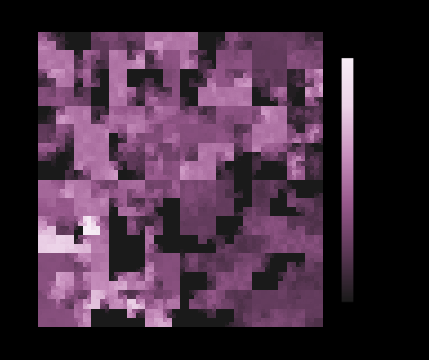

```mathematica
hilbertCurveEntropyView[inputFile["notepad++.exe"],8,1700000]
```